True

{0.000098454,0.00275183,0.00161586,0.00307943,-0.00236619,-0.000617567,0.000991499,-0.000745601,0.00311153,-0.00196234,0.00327928,-0.000415219,-0.000269817,-0.00111105,0.00473596,0.00194189,-0.000448859,-0.00079252,0.00374845,0.00114025,0.000716269,-0.000589029,0.00158831,0.00197558,0.00449421,-0.000268776,0.00313589,0.00330351,-0.000307267,0.00169831}

{0.00471375,0.000624585,0.000437134,0.00121038,0.00117179,0.00241607,0.00272897,0.00320621,0.00225003,0.00234988,0.00149748,0.00158736,0.00150701,0.000948397,-0.00172287,0.000129178,0.000337284,0.00137735,0.00102734,0.000800449,0.000610146,-0.00108255,-0.000449148,0.000446868,-0.000816123,0.000398,0.000542653,-0.000234991,-0.000867683,0.00120329}

Vwap no error test for normality:

| Statistic | P-Value
Kolmogorov-Smirnov | 0.166211 | 0.0349228

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is rejected at the 5. percent level based on the Kolmogorov-Smirnov test.

Vwap error test for normality:

| Statistic | P-Value
Kolmogorov-Smirnov | 0.114343 | 0.402416

The null hypothesis that the data is distributed according to the NormalDistribution[x,y] is not rejected at the 5. percent level based on the Kolmogorov-Smirnov test.

True

| Statistic | P-Value
Mann-Whitney | 473. | 0.739399

The null hypothesis that the median difference is 0 is not rejected at the 5. percent level based on the Mann-Whitney test.

| Statistic | P-Value
T | 0.39874 | 0.691724

The null hypothesis that the mean difference is 0 is not rejected at the 5. percent level based on the T test.

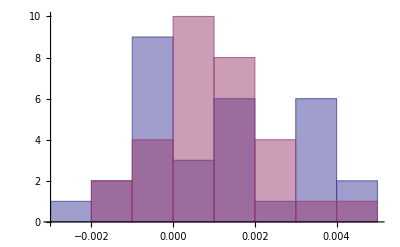

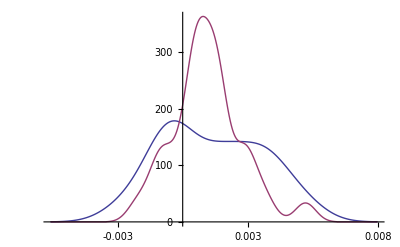

```mathematica
ClearAll[vwapnoerror, vwaperror,vwapnoerrordiff, vwaperrordiff];
(* buying 40000 over 12 minutes*)
(* 5 equal targets *)
(*vwapnoerror={
{96.0313, 96.7136},
{102.351, 102.001},
{98.4604, 100.001},
{104.348, 103.467},
{102.527,101.668 },
{99.1499, 99.4798},
{99.8478,100.12 },
{103.341, 102.149},
{105.445, 103.732},
{99.2266, 99.749},
{104.054, 103.726},
{99.586,100.052},
{103.561, 101.489},
{105.095,104.326},
{92.2076, 93.0652},
{93.7433, 94.285},
{94.6753, 95.664},
{102.281, 102.079},
{96.9573, 97.1044},
{92.1517, 92.32},
{103.798,103.642},
{93.8098, 94.6338},
{98.3321, 98.5782},
{100.719, 100.773},
{95.5796, 96.1158},
{98.8483, 98.7892},
{101.916,101.656},
{106.095, 104.623},
{107.78, 107.292},
{105.561, 104.507}
};*)

(* 10 equal targets *)
(*vwaperror={
{98.883, 99.0799},
{103.498, 103.245},
{97.0235, 97.2669},
{98.0981, 98.6341},
{102.008, 101.896},
{96.7254, 96.6508},
{103.533, 103.22},
{102.84, 102.679},
{98.0757, 97.5122},
{100.862, 101.116},
{107.904, 107.463},
{103.151, 103.089},
{104.681, 104.493},
{98.7469, 98.4905},
{102.858, 103.094},
{101.653, 100.984},
{101.034, 100.602},
{95.3543, 95.3018},
{99.7209, 99.4824},
{109.882,109.356},
{104.136, 103.855},
{98.304, 97.9769},
{106.422, 105.555},
{99.08, 99.2462},
{103.636, 103.368},
{100.364, 100.363},
{103.301,103.116},
{103.374, 102.732},
{106.079, 106.141},
{99.5319, 99.5495},
{104.367, 103.559},
{98.2278, 98.5039},
{95.3533, 95.8091},
{96.8531, 97.4147},
{99.3296, 99.2665},
{101.755, 101.252},
{103.998, 103.743}
};
*)

(* 20 equal targets *)
vwapnoerror={
{98.5232,98.5135},
{106.838, 106.544},
{98.9563, 98.7964},
{105.539, 105.214},
{97.5407, 97.7715},
{100.394, 100.456},
{101.866, 101.765},
{100.59, 100.665},
{109.271, 108.931},
{96.3646, 96.5537},
{105.206, 104.861},
{97.2981, 97.3385},
{100.068, 100.095},
{95.2251, 95.3309},
{102.408,101.923 },
{106.082, 105.876},
{94.4618, 94.5042},
{99.4297, 99.5085},
{107.778, 107.374},
{102.609, 102.492},
{101.917,101.844},
{97.109, 97.1662},
{102.625,102.462},
{103.261, 103.057},
{106.804, 106.324},
{104.176, 104.204},
{106.19, 105.857},
{105.948, 105.598},
{104.144, 104.176},
{101.866, 101.693}
};

(* 40 equal targets *)
vwaperror = {
{108.194, 107.684},
{98.9457, 98.8839},
{105.231, 105.185},
{101.621, 101.498},
{100.103, 99.9857},
{106.371, 106.114},
{99.4514, 99.18},
{109.163, 108.813},
{111.554, 111.303},
{102.984, 102.742},
{104.843, 104.686},
{102.056, 101.894},
{102.853, 102.698},
{100.169, 100.074},
{93.9133, 94.0751},
{100.636, 100.623},
{106.735, 106.699},
{106.727,106.58},
{104.152, 104.045},
{93.6974, 93.6224},
{101.615, 101.553},
{104.383, 104.496},
{99.9671, 100.012},
{97.3442, 97.3007},
{104.151, 104.236},
{103.015, 102.974},
{108.725, 108.666},
{96.5993, 96.622},
{95.0808, 95.1633},
{101.389, 101.267}(*,
{100.773, 100.599},
{104.63, 104.576},
{107.473,107.006 },
{106.656, 106.415},
{103.745, 103.422},
{100.948, 100.979},
{97.5779, 97.6888}*)
};

Length[vwapnoerror]==Length[vwaperror]

(*vwapnoerrordiff = #[[1]]-#[[2]]&/@vwapnoerror
vwaperrordiff = #[[1]]-#[[2]]&/@vwaperror*)

vwapnoerrordiff = 1-#[[2]]/#[[1]]&/@vwapnoerror
vwaperrordiff = 1-#[[2]]/#[[1]]&/@vwaperror


Print["Vwap no error test for normality:"];
Print[KolmogorovSmirnovTest[vwapnoerrordiff ,Automatic,"TestDataTable"]];
Print[KolmogorovSmirnovTest[vwapnoerrordiff ,Automatic,"TestConclusion"]];

Print["Vwap error test for normality:"];
Print[KolmogorovSmirnovTest[vwaperrordiff ,Automatic,"TestDataTable"]];
Print[KolmogorovSmirnovTest[vwaperrordiff ,Automatic,"TestConclusion"]];

Length[vwapnoerrordiff]==Length[vwaperrordiff]


Print[MannWhitneyTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestDataTable"]];
Print[MannWhitneyTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestConclusion"]];

Print[TTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestDataTable"]];
Print[TTest[{vwapnoerrordiff, vwaperrordiff},Automatic,"TestConclusion"]];

Histogram[{vwapnoerrordiff, vwaperrordiff}]
SmoothHistogram[{vwapnoerrordiff, vwaperrordiff}]
```